55

30

17

13

10

65.113

55

30

1/17

1/13

1/10

0.0153579

-17/x-(65.113 (-13/x+55 x-(30 x)/(-1+3 x^2)))/(x (-78.113/x+55 x-(30 x)/(-1+3 x^2)))

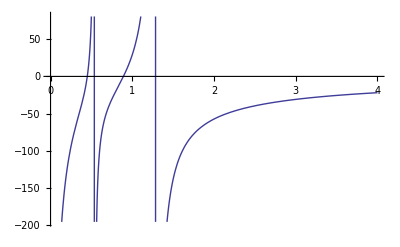

F1=

0.151105 x-0.938346 x^3+0.941534 x^5

F1=0:

{{x→-0.891435},{x→-0.449398},{x→0.},{x→0.449398},{x→0.891435}}

F2=

0.00542829 x^2-0.0221918 x^4+0.0114663 x^6

F2=0:

{{x→-1.2838},{x→-0.535946},{x→0.},{x→0.},{x→0.535946},{x→1.2838}}

-(0.151105 x-0.938346 x^3+0.941534 x^5)/(0.00542829 x^2-0.0221918 x^4+0.0114663 x^6)

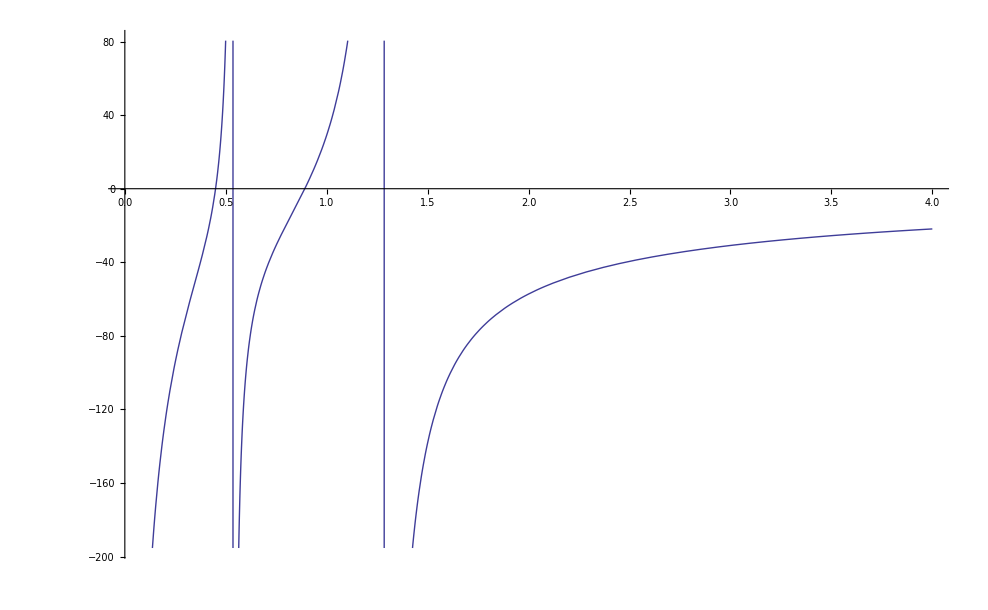

Solve::ivar: 0 is not a valid variable.

```mathematica
XL1=55
XL3=30
XC1=17
XC2=13
XC3=10
XC4=65.113
L1=XL1
L3=XL3
C1=1/XC1
C2=1/XC2
C3=1/XC3
C4=1/XC4
G=-1/(C1 x)-(-1/(C2 x)-(L3 x)/(C3 L3 x^2-1)+L1 x)/((C4 x) (-1/(C2 x)-(L3 x)/(C3 L3 x^2-1)-1/(C4 x)+L1 x))
Plot[G,{x,0,+4}]
"F1="  
K1=C2 C3 L1 L3 x^5 (C1+C4)-x^3 ((C1+C4) (C2 L1+C2 L3+C3 L3)+C2 C3 L3)+x (C1+C2+C4)
"F1=0: "    
Solve[K1==0,x]
"F2="  
K2=C1 C2 C3 C4 L1 L3 x^6-C1 x^4 (C4 (C2 L1+C2 L3+C3 L3)+C2 C3 L3)+C1 x^2 (C2+C4)
"F2=0: " 
Solve[K2==0,x]
K=-K1/K2
Plot[K,{x,0,4}]
```